# Лабораторная работа №2

## Лабораторная работа №2. Символьные вычисления в системе MATHEMATICA.

## 1

### 1.1

Придумайте и определите выражение, содержащее не менее трех слагаемых, причем хотя бы одно из них должно быть рациональным выражением.

```mathematica
t1 =/((x^2+4) (x+y))+x+y+(x+y)^2;
```

Последовательно примените к нему функции Expand, ExpandAll, Factor, Together, Apart, Cancel, Simplify и объясните их действие. Выражение t1 должно быть таким, чтобы можно было проследить работу каждой из этих функций.
Функция Expand раскрывает скобки в выражении и представляет результат в виде суммы.

```mathematica
Expand[t1]
```

x+x^2+y+2 x y+y^2-(8 x^2)/((4+x^2) (x+y))+(2 x^4)/((4+x^2) (x+y))+(8 y^2)/((4+x^2) (x+y))-(2 x^2 y^2)/((4+x^2) (x+y))

Функция ExpandAll расширяет все произведения и целые степени в любой части выражения.

```mathematica
ExpandAll[t1]
```

x+x^2+y+2 x y+y^2-(8 x^2)/(4 x+x^3+4 y+x^2 y)+(2 x^4)/(4 x+x^3+4 y+x^2 y)+(8 y^2)/(4 x+x^3+4 y+x^2 y)-(2 x^2 y^2)/(4 x+x^3+4 y+x^2 y)

Функция Factor факторизирует полином над целыми числами.

```mathematica
Factor[t1]
```

(-4 x+4 x^2+3 x^3+x^4+12 y+8 x y-x^2 y+2 x^3 y+4 y^2+x^2 y^2)/(4+x^2)

Функция Together складывает члены в сумму по общему знаменателю и отменяет множители в результате.

```mathematica
Together[t1]
```

(-4 x+4 x^2+3 x^3+x^4+12 y+8 x y-x^2 y+2 x^3 y+4 y^2+x^2 y^2)/(4+x^2)

Функция Apart переписывает рациональное выражение как сумму терминов с минимальными знаменателями.

```mathematica
Apart[t1]
```

(x (-4+4 x+3 x^2+x^3))/(4+x^2)+((12+8 x-x^2+2 x^3) y)/(4+x^2)+y^2

Функция Cancel убирает общие множители в числителе и знаменателе выражения.

```mathematica
Cancel[t1]
```

x+(2 (-4+x^2) (x-y))/(4+x^2)+y+(x+y)^2

Функция Simplify выполняет последовательность алгебраических и других преобразований выражения и возвращает простейшую найденную форму.

```mathematica
Simplify[t1]
```

x+(2 (-4+x^2) (x-y))/(4+x^2)+y+(x+y)^2

### 1.2

Приведите выражение t1 к общему знаменателю и с помощью функции Numerator определите числитель полученного выражения, обозначив его t2. С помощью функции Collect представьте выражение t2 в виде полинома по x или y. Определите максимальную степень n одной из переменных, например, x в выражении t2 и коэффициент при x^n. Используйте функции Exponent и Coefficient.

```mathematica
t2 = Numerator[Together[t1]]
Collect[t2,x]
Exponent[t2,x]
Coefficient[t2,x,Exponent[t2,x]]
```

-4 x+4 x^2+3 x^3+x^4+12 y+8 x y-x^2 y+2 x^3 y+4 y^2+x^2 y^2

x^4+12 y+4 y^2+x^3 (3+2 y)+x (-4+8 y)+x^2 (4-y+y^2)

4

1

## 2

### 2.1

С помощью функции D вычислите производную функции x^n cosx.

```mathematica
D[x^n Cos[x],x]
```

n x^(-1+n) Cos[x]-x^n Sin[x]

### 2.2

Вычислите производные.

```mathematica
D[(a x^3+2 x^2),x]
```

4 x+3 a x^2

```mathematica
D[4 x^2-5 x+8-3/x,{x,3}]
```

18/x^4

```mathematica
D[x^3 y^2+3 x^2,{x,3},{y,2}]
```

12

### 2.3

Используя функцию Integrate, вычислите интеграл.

```mathematica
Integrate[1/(x^2-1),x]
```

1/2 Log[1-x]-1/2 Log[1+x]

### 2.4

Вычислите интегралы, затем продифференцируйте полученные выражения и убедитесь в том, что получаемые результаты совпадают с подынтегральными выражениями. При необходимости используйте функции для преобразования выражений.

```mathematica
Together[D[Integrate[x^3/(x^2+1),x],x]]                                              (* x*(1+x^2)-x = x+x^3-x = x^3 *)
```

x^3/(1+x^2)

```mathematica
Simplify[D[Integrate[1/(x^3+1),x],x]]                                              (* (1+x)(1-x+x^2) = 1-x+x^2+x-x^2+x^3*)
```

1/(1+x^3)

### 2.5

Вычислите определенный интеграл.

```mathematica
Integrate[5 x-2 √x+32/x^3,{x,1,4}]
```

259/6

### 2.6

Вычислите интегралы.

```mathematica
Integrate[(1+x^4)^(1/3),{x,0,1}]
Integrate[(1+x^4)^(1/3),{x,0,1.}]
```

Hypergeometric2F1[-1/3,1/4,5/4,-1]

1.05753

## 3

### 3.1

Используя функцию Solve, решить уравнение ax^4 + x^2 + 3 = 0.

```mathematica
Solve[a x^4+x^2+3==0,x]
```

{{x→-(√(-1/a-(√(1-12 a))/a))/(√2)},{x→(√(-1/a-(√(1-12 a))/a))/(√2)},{x→-(√(-1/a+(√(1-12 a))/a))/(√2)},{x→(√(-1/a+(√(1-12 a))/a))/(√2)}}

### 3.2

Найти точное решение системы уравнений.

```mathematica
Solve[{x^2+y==1,y^2-x^2==2},{x,y}]
```

{{x→-ⅈ √(1/2 (-3+√13)),y→1/2 (-1+√13)},{x→ⅈ √(1/2 (-3+√13)),y→1/2 (-1+√13)},{x→-√(1/2 (3+√13)),y→1/2 (-1-√13)},{x→√(1/2 (3+√13)),y→1/2 (-1-√13)}}

### 3.3

Решить систему уравнений.

```mathematica
Solve[{x^2-y^2==1,y^3+x==5},{x,y}]
```

{{x→5-(Root1.48Root[24-#1^2-10 #1^3+#1^6&,1]1.4762125973105025)^3,y→Root1.48Root[24-#1^2-10 #1^3+#1^6&,1]1.4762125973105025},{x→5-(Root1.93Root[24-#1^2-10 #1^3+#1^6&,2]1.9285042654455715)^3,y→Root1.93Root[24-#1^2-10 #1^3+#1^6&,2]1.9285042654455715},{x→5-(Root-0.914-1.30 ⅈRoot[24-#1^2-10 #1^3+#1^6&,3]-0.91389935476702)^3,y→Root-0.914-1.30 ⅈRoot[24-#1^2-10 #1^3+#1^6&,3]-0.91389935476702},{x→5-(Root-0.914+1.30 ⅈRoot[24-#1^2-10 #1^3+#1^6&,4]-0.91389935476702)^3,y→Root-0.914+1.30 ⅈRoot[24-#1^2-10 #1^3+#1^6&,4]-0.91389935476702},{x→5-(Root-0.788-1.65 ⅈRoot[24-#1^2-10 #1^3+#1^6&,5]-0.788459076611017)^3,y→Root-0.788-1.65 ⅈRoot[24-#1^2-10 #1^3+#1^6&,5]-0.788459076611017},{x→5-(Root-0.788+1.65 ⅈRoot[24-#1^2-10 #1^3+#1^6&,6]-0.788459076611017)^3,y→Root-0.788+1.65 ⅈRoot[24-#1^2-10 #1^3+#1^6&,6]-0.788459076611017}}

### 3.4

Найдите общие решения дифференциальных уравнений, используя функцию DSolve.

```mathematica
res = DSolve[y'[x]-y[x] Tan[x]==x,y[x],{x,0,1}]
```

{{y[x]→1+C[1] Sec[x]+x Tan[x]}}

```mathematica
res2 = DSolve[y'[x]+y[x] Tan[x]==1/Cos[x],y[x],{x,0,1}]
```

{{y[x]→C[1] Cos[x]+Sin[x]}}

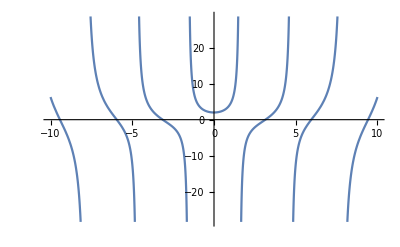

```mathematica
Plot[Evaluate[y[x]/.res/.{C[1]->1}],{x,-10,10}]
```

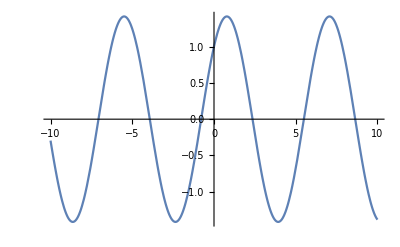

```mathematica
Plot[Evaluate[y[x]/.res2/.{C[1]->1}],{x,-10,10}]
```

### 3.5

Самостоятельно выбрав граничные условия, найдите решение дифференциального уравнения в символьном виде. Затем с помощью функции NDSolve найдите численное решение этого уравнения. Интервал изменения x выберите самостоятельно. На одной координатной плоскости постройте графики численного и символьного решений и покажите, что они совпадают.

```mathematica
res3 = DSolve[{y''[x]-y'[x]+x y[x]==0,y[0]==1,y'[0]==1},y[x],{x,-10,10}]
```

{{y[x]→(ⅇ^(x/2) (((-1)^(2/3) AiryAi[-1/4 (-1)^(1/3)]+2 AiryAiPrime[-1/4 (-1)^(1/3)]) AiryBi[1/4 (-1)^(1/3) (-1+4 x)]-AiryAi[1/4 (-1)^(1/3) (-1+4 x)] ((-1)^(2/3) AiryBi[-1/4 (-1)^(1/3)]+2 AiryBiPrime[-1/4 (-1)^(1/3)])))/(2 AiryAiPrime[-1/4 (-1)^(1/3)] AiryBi[-1/4 (-1)^(1/3)]-2 AiryAi[-1/4 (-1)^(1/3)] AiryBiPrime[-1/4 (-1)^(1/3)])}}

```mathematica
res4 = NDSolve[{y''[x]-y'[x]+x y[x]==0,y[0]==1,y'[0]==1},y[x],{x,-10,10}]
```

{{y[x]→InterpolatingFunction[…][x]}}

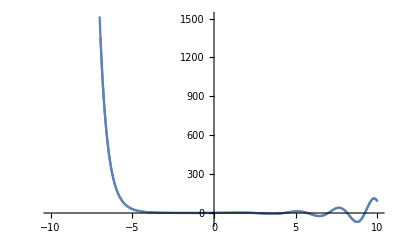

```mathematica
Show[Plot[y[x]/.res3,{x,-10,10}], Plot[y[x]/.res4, {x, -10, 10}]]
```